# S_n-equivariant weight zero compactly supported Euler characteristic of H_gn

## Computation of S_n-equivariant weight zero Euler characteristic of H_gn.

# Code

## Step 1. Compute the (relevant) trees.

### The main command in this step is RelevantTrees[g], which for a given genus g, gives all trees with 2g+2 leaves outside the weight 3 locus, and also outside the evenVeven / evenUeven locus.

#### makeTree Input: undesirable TreeForm object Output: a graph which is the tree

```mathematica
makeTree[nodes_]:=Module[{counter=0},traverse[h_[childs___]]:=With[{id=counter},{UndirectedEdge[id,++counter],traverse[#]}&/@{childs}];
traverse[_]:=Sequence[];
Graph[#]&@Flatten[traverse[nodes]]]
```

#### InteriorEdges

```mathematica
InteriorEdges[T_]:=Module[{newT},
newT=T;
For[j=1,j≤Length[Leaves[T]],j=j+1,
newT=VertexDelete[newT,Leaves[T][[j]]]
];
Return[EdgeList[newT]];
];
```

#### Contractions: produces all the children of a tree

```mathematica
Contractions[T_]:=DeleteDuplicates[Table[EdgeContract[T,InteriorEdges[T][[i]]],{i,1,Length[InteriorEdges[T]]}],IsomorphicGraphQ[#1,#2]&]
```

#### KillWeight3[L]: removes all trees in a list L of trees that are in the weight 3 locus

```mathematica
KillWeight3[L_]:=DeleteCases[L,T_/;
MemberQ[Table[CountLeaves[T,VertexList[T][[i]]]≥3,{i,1,Length[VertexList[T]]}],True]]
```

#### Leaves Input: a tree Output: set of vertices of valence 1.

```mathematica
Leaves[T_]:=Select[VertexList[T],VertexDegree[T,#]==1&]
```

#### CountLeaves Input: a tree and a vertex Output: the number of leaf vertices adjacent to that vertex.

```mathematica
CountLeaves[T_,v_]:=Module[{n,j},
n=0;
For[j=1,j≤Length[Leaves[T]],j=j+1,
If[EdgeQ[T,v<->Leaves[T][[j]]],n=n+1,n=n]
];
Return[n]
]
```

#### isevenVeven input: tree output: true if the tree contains ____even____V_____even___

```mathematica
evenVevenVertex[T_,v_]:=Module[{},
If[CountLeaves[T,v]==2,
If[VertexDegree[T,v]==4,
If[
EvenQ/@Length/@Leaves/@DeleteCases[ConnectedGraphComponents[VertexDelete[T,v]],c_/;Length[VertexList[c]]==1]=={True,True},Return[True]
,Return[False]]
,Return[False]]
];
Return[False];
]
```

```mathematica
evenVeven[T_]:=MemberQ[Table[evenVevenVertex[T,VertexList[T][[i]]],{i,1,Length[VertexList[T]]}],True]
```

#### isevenUeven input : tree ouptut : true if the tree contains __even __ | ___ _ | ___even ___

```mathematica
isleafvertex[T_,v_]:=If[VertexDegree[T,v]==3,If[CountLeaves[T,v]==1,Return[True],Return[False]],Return[False]]
```

```mathematica
isbridgeedge[T_,e_]:=If[Length[DeleteCases[ConnectedComponents[EdgeDelete[T,e]],c_/;Length[c]==1]]==2,Return[True],Return[False]]
```

```mathematica
isevenUevenEdge[T_,e_]:=If[isbridgeedge[T,e]==True,
If[
isleafvertex[T,e[[1]]]==True,
If[
isleafvertex[T,e[[2]]]==True,
If[
OddQ/@Length/@Leaves/@ConnectedGraphComponents[EdgeDelete[T,e]]=={True,True},
Return[True],Return[False]
],Return[False]
],Return[False]
],Return[False]
]
```

```mathematica
evenUeven[T_]:=MemberQ[Table[isevenUevenEdge[T,EdgeList[T][[i]]],{i,1,Length[EdgeList[T]]}],True]
```

#### Relevant Trees[g]: trees with 2g+2 leaves outside the weight 3 locus, and also outside the evenVeven / evenUeven locus.

```mathematica
RelevantTrees[g_]:=Module[{AllMaxRootedTrees,AllMaxTrees,RelevantTrees,parents,children,n},
n=2g+2;
AllMaxRootedTrees=makeTree/@TreeForm/@Groupings[Table[a,n-1],{2,Orderless}];
AllMaxTrees=DeleteDuplicates[AllMaxRootedTrees,IsomorphicGraphQ[#1,#2]&];
RelevantTrees=AllMaxTrees;
parents=AllMaxTrees;
While[Length[parents]>0,
children = DeleteDuplicates[KillWeight3[Flatten[Contractions/@parents]],IsomorphicGraphQ[#1,#2]&];
RelevantTrees=Join[RelevantTrees,children];
parents=children
];
Return[DeleteCases[DeleteCases[RelevantTrees,t_/;evenVeven[t]==True],t_/;evenUeven[t]==True]](*this does the evenVeven / evenUeven reduction*)
]
```

## Step 2. Turn the trees into hyperelliptic graphs

### The main command at this step is Contributors[g], which lists all hyperelliptic graphs coming from RelevantTrees[g].

#### Prune Input: a tree and a root Output: a tree where all leaves have been removed, leave behind on each edge the “slope” and on each vertex the count of leaves on that vertex.

```mathematica
Prune[T_,r_]:=Module[{newT,vlabels,elabels,j,IntV,k,e,delT,P,notroots},
vlabels={};
elabels={};
newT=T;
For[j=1,j≤Length[Leaves[T]],j=j+1,
newT=VertexDelete[newT,Leaves[T][[j]]]
];
IntV = Select[VertexList[T],VertexDegree[T,#]>1&];
For[k=1,k≤Length[IntV],k=k+1,
AppendTo[vlabels,IntV[[k]]->CountLeaves[T,IntV[[k]]]]
];
notroots=DeleteCases[VertexList[newT],r];
For[e=1,e≤Length[notroots],e=e+1,
P=FindShortestPath[T,notroots[[e]],r];
delT=ConnectedComponents[EdgeDelete[T,P[[1]]<-> P[[2]]],{notroots[[e]]}];
AppendTo[elabels,P[[1]]<-> P[[2]]->Sum[CountLeaves[T,delT[[1,l]]],{l,1,Length[delT[[1]]]}]];
];
Return[Graph[EdgeList[newT],VertexLabels->vlabels,EdgeLabels->elabels]];
];
```

#### PossibleT Input: a tree Output: look at all choices of root. Make the corresponding “pruned” trees.

```mathematica
PossibleT[T_]:=Module[{newTs,IntV},
IntV = Select[Select[VertexList[T],VertexDegree[T,#]>1&],CountLeaves[T,#]>0&][[1]];
newTs=Prune[T,IntV];
Return[{newTs}];
]
```

#### VertexLabelGet, EdgeLabelGet Input: a graph G Output: a list of pairs {v,l} of a vertex(edge) and its label

```mathematica
EdgeLabelGet[G_]:=List@@@PropertyValue[G,EdgeLabels]
VertexLabelGet[G_]:=List@@@PropertyValue[G,VertexLabels]
```

#### PrunedTrees Input: g Output: all the pruned trees on 2g+2 leaves

```mathematica
PrunedTrees[g_]:=Module[{possible,theguyslab,theguysunlab,i,tester,j,tab,trees},
trees=RelevantTrees[g];
possible=Flatten[Table[PossibleT[trees[[j]]],{j,1,Length[trees]}]];
Return[possible]
]
```

#### SplitVertiecs Input: T, a pruned tree Output: a list of the vertices which will have 2 preimages in the graph G

```mathematica
SplitVertices[T_]:=Module[{SplitEdges,neighbors,v,i,tab,splitV,labels,n,d},
d=2;
SplitEdges=DeleteCases[Flatten[Select[EdgeLabelGet[T],Divisible[#[[2]],d]&]],_Integer];
splitV={};
labels=VertexLabelGet[T];
For[i=1,i≤Length[labels],i=i+1,
v=labels[[i,1]];
neighbors=EdgeList[T,v<->_];
n=labels[[i,2]];
tab=Table[EdgeQ[Graph[SplitEdges],neighbors[[j]]],{j,1,Length[neighbors]}];
If[MemberQ[tab,False]==False,
If[n==0,AppendTo[splitV,v]]
]
];
Return[splitV]
]
```

#### MakeGraph Input: a pruned T, g Output: the graph

```mathematica
MakeGraph[T_,g_]:=Module[{G,SplitEdges,i,vlabels,splitVs,k,edgestodo,newvs,nonsplits,m,nosplitVs,e,oldlabels,v,w,nm,oldlabel,d,numleaves},
numleaves=2g+2;
d=2;
vlabels={};
G={};
SplitEdges=DeleteCases[Flatten[Select[EdgeLabelGet[T],Divisible[#[[2]],d]&]],_Integer];
splitVs=SplitVertices[T];
nosplitVs=Complement[VertexList[T],splitVs];
nonsplits=If[Length[SplitEdges]==0,EdgeList[T],EdgeList[EdgeDelete[T,SplitEdges]]];
AppendTo[G,nonsplits];
For[i=1,i≤Length[SplitEdges],i=i+1,
e=SplitEdges[[i]];
(*case 1: no vertices split*)
If[Not[Or[MemberQ[splitVs,e[[1]]],MemberQ[splitVs,e[[2]]]]],
AppendTo[G,Table[e,{o,1,d}]],
(*case 2: both split*)
If[And[MemberQ[splitVs,e[[1]]],MemberQ[splitVs,e[[2]]]],
AppendTo[G,Table[{e[[1]],n}<->{e[[2]],n},{n,1,d}]],
(*case 3: one splits, divided into whether it is v1 or v2*)
If[MemberQ[splitVs,e[[1]]],
AppendTo[G,Table[{e[[1]],n}<->e[[2]],{n,1,d}]],
AppendTo[G,Table[{e[[2]],n}<->e[[1]],{n,1,d}]]
]
]
];
];
oldlabels=VertexLabelGet[T];
For[m=1,m≤Length[nosplitVs],m=m+1,
v=nosplitVs[[m]];
oldlabel=Flatten[Select[VertexLabelGet[T],#[[1]]==v&]][[2]];
nm=oldlabel+ If[MemberQ[VertexList[Graph[nonsplits]],v],Length[AdjacencyList[Graph[nonsplits],v]],0];
w=(d-1)(nm-2)/2;
If[w≠0,AppendTo[vlabels,{v->w}]]
];
Return[Graph[Flatten[G],VertexLabels->Flatten[vlabels]]];
];
```

#### Contributors Input: g the genus Output: a graphic of all of the graphs which contribute to Z_g

```mathematica
Contributors[g_]:=Module[{trees,T,L,k},
trees=PrunedTrees[g];
T=Table[MakeGraph[trees[[i]],g],{i,1,Length[trees]}];
Return[T];
]
```

## Step 3. Compute the contribution to h_g of each graph

### The main command is Contribution[G], which gives the contribution to h_g from a specific hyperelliptic graph G.

## installingIGraph/M Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]

```mathematica
<<IGraphM`
```

IGraph/M 0.5.1 (October 12, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
IGVersion[]
```

IGraph/M 0.5.1 (October 12, 2020)
igraph 0.9.0-pre+6969bf6bc (Oct 12 2020)
Mac OS X x86 (64-bit)

#### Find the “canonical” presentation of the graph, with half edges

```mathematica
SubDivide[G_]:=Module[{newedges,v,colors,v2,labels},
newedges={};
For[i=1,i≤Length[EdgeList[G]],i=i+1,
v=RandomReal[];
newedges=Union[newedges,{v<->EdgeList[G][[i,1]],v<->EdgeList[G][[i,2]]}]
];
colors=Table[VertexLabelGet[G][[i,1]]->{"color"->VertexLabelGet[G][[i,2]]},{i,1,Length[VertexLabelGet[G]]}];
Return[Graph[newedges,Properties->colors]]
]
```

#### Compute the (edge) automorphism group, respecting vertex weights

```mathematica
Aut[G_]:=IGBlissAutomorphismGroup[{G,"VertexColors"->IGVertexProp["Color"][G]}]
```

#### Find quotient graph given an automorphism

```mathematica
QuotientGraph[G_,tau_]:=Module[{group,vertices,edgeorbits,edges},
group = PermutationGroup[{tau}];
vertices= GroupOrbits[group,VertexList[G]];
edgeorbits=Sort/@VertexList/@Graph/@GroupOrbits[group,EdgeList[G]];
edges=DeleteCases[Flatten[Table[Table[vertices[[i]]<->vertices[[j]],{k,1,Count[edgeorbits,Union[vertices[[i]],vertices[[j]]]]}]
,{i,1,Length[vertices]},{j,i+1,Length[vertices]}]],{}];
Return[Graph[edges]]
]
```

#### Computes the involution of G

```mathematica
Involution[G_]:=Module[{order2,maxval},
order2=DeleteCases[GroupElements[Aut[G]],x_/;PermutationOrder[x]!=2];
Return[DeleteCases[order2,x_/;TreeGraphQ[QuotientGraph[G,x]]==False]];
]
```

#### Number of edges in the tree associated to G (this number gets divided by 2 later)

```mathematica
LengthET[G_]:=Length[GroupOrbits[PermutationGroup[Involution[G]],EdgeList[G]]]
```

#### Tree of G

```mathematica
T[G_]:=QuotientGraph[G,Involution[G][[1]]]
```

#### Determine the sign of the automorphism. SGN[G,tau]

```mathematica
SGN[G_,tau_]:=Module[{badorbits,orbits},
badorbits = GroupOrbits[PermutationGroup[{tau}],EdgeList[T[G]]];
orbits=DeleteDuplicates[ Table[Sort[
DeleteDuplicates[Table[Sort[{Sort[badorbits[[i,j,1]]],Sort[badorbits[[i,j,2]]]}],{j,1,Length[badorbits[[i]]]}]]]
,{i,1,Length[badorbits]}]];
Return[If[EvenQ[Length[DeleteCases[Length/@orbits,x_/;OddQ[x]==True]]],
(-1)^(Length[DeleteCases[Length/@orbits,x_/;OddQ[x]==True]]/2),
(-1)^((Length[DeleteCases[Length/@orbits,x_/;OddQ[x]==True]]-1)/2)
]]
]
```

#### contribution from a G, tau

```mathematica
ContributionTau[G_,tau_]:=Module[{edgelist,badedgeorbits,edgeorbits,vertexorbits},
edgeorbits=DeleteDuplicates[DeleteDuplicates/@Map[Sort,GroupOrbits[PermutationGroup[{tau}],EdgeList[G]],2]];
vertexorbits=GroupOrbits[PermutationGroup[{tau}],VertexList[G]];
Return[SGN[G,tau]*Product[P[Length[vertexorbits[[i]]]],{i,1,Length[vertexorbits]}]*Product[P[Length[edgeorbits[[i]]]]^(-1),{i,1,Length[edgeorbits]}]]
]
```

#### compute conjugacy classes of a group

```mathematica
ConjugacyClasses[G_]:=Module[{elements,classes,currentclass},
elements=GroupElements[G];
classes={};
While[Length[elements]>0,
currentclass=Flatten[GroupOrbits[G,{elements[[1]]}]];
classes=Append[classes,currentclass];
elements=Complement[elements,currentclass]
];
Return[classes]
]
```

#### Contribution from a G

```mathematica
Contribution[G_]:=((-1)^(Length[EdgeList[T[G]]]/2)/GroupOrder[Aut[G]])*Sum[
Length[ConjugacyClasses[Aut[G]][[i]]]*ContributionTau[G,ConjugacyClasses[Aut[G]][[i,1]]]
,{i,1,Length[ConjugacyClasses[Aut[G]]]}]
```

## Step 4. Add them all up

```mathematica
h[g_]:=Module[{contributors},
contributors=Contributors[g];
Simplify[Sum[Contribution[Graph[IGBlissCanonicalGraph[{SubDivide[contributors[[i]]],"VertexColors"->"color"}]]],{i,1,Length[contributors]}]]
]
```

```mathematica
hstatus[g_]:=Module[{contributors,i,hg},
contributors=Contributors[g];
hg=0;
For[i=0,i<Length[contributors],i=i+1;
Print[i];
hg=hg+Contribution[Graph[IGBlissCanonicalGraph[{SubDivide[contributors[[i]]],"VertexColors"->"color"}]]];
];
Return[Simplify[hg]]
]
```

```mathematica
hstatus2[g_]:=Module[{contributors,i,hg},
contributors=Contributors[g];
Print[Length[contributors]];
hg=0;
For[i=0,i<Length[contributors],i=i+1;
If[Mod[i,10]==0,Print[i]];
hg=hg+Contribution[Graph[IGBlissCanonicalGraph[{SubDivide[contributors[[i]]],"VertexColors"->"color"}]]];
];
Return[Simplify[hg]]
]
```

# Computations

## Contributors for g=2,3

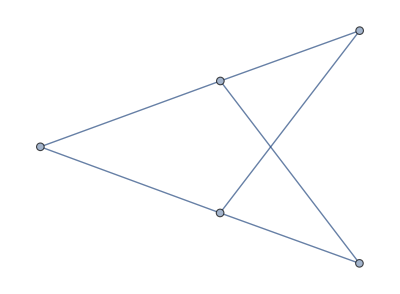

```mathematica
Contributors[2]
```

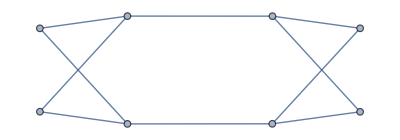
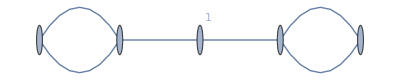
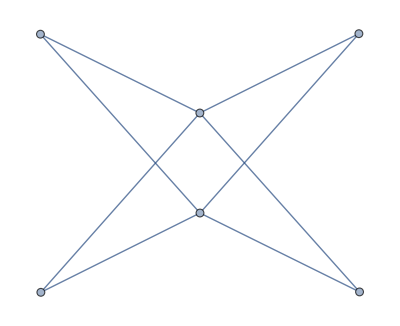
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Contributors[3]
```

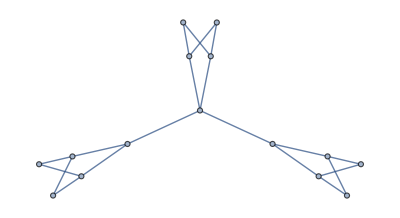
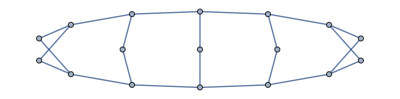
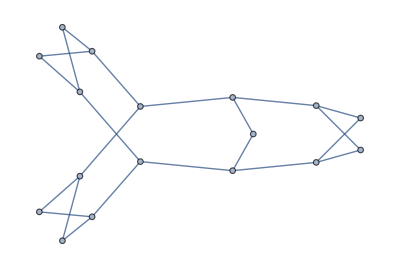
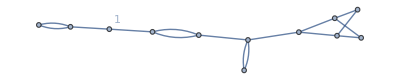
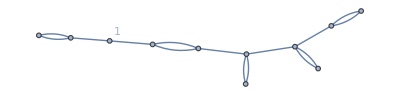
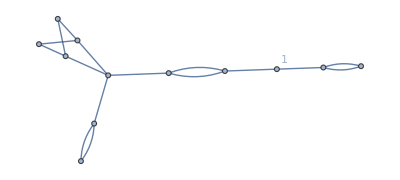
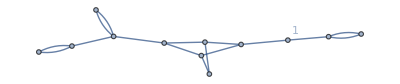
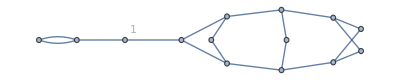
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Contributors[6]
```

## Computing h_g for g=2,3,4,5,6,7

### h[2] (don’t mind the warnings from IGraphM)

```mathematica
h[2]
```

IGraphM::vcolm: The vertex property color does not contain any values. Assuming all vertices to have the same color.

1/12 (-1/P[1]-P[1]^3/P[2]^2+(6 P[1])/P[2]-(2 P[1]^2)/P[3]-(2 P[2] P[3])/P[6])

```mathematica
h2=1/12 (-1/P[1]-P[1]^3/P[2]^2+(6 P[1])/P[2]-(2 P[1]^2)/P[3]-(2 P[2] P[3])/P[6]);
```

### h[3]

```mathematica
h[3]
```

IGraphM::vcolm: The vertex property color does not contain any values. Assuming all vertices to have the same color.

General::stop: Further output of IGraphM::vcolm will be suppressed during this calculation.

-((P[1]^2+P[2]-2 P[1] P[2]) (P[1]^4 P[4]+P[2]^2 P[4]+2 P[1]^2 (P[2]^3+2 P[2] P[4])))/(16 P[1]^2 P[2]^3 P[4])

```mathematica
h3=-((P[1]^2+P[2]-2 P[1] P[2]) (P[1]^4 P[4]+P[2]^2 P[4]+2 P[1]^2 (P[2]^3+2 P[2] P[4])))/(16 P[1]^2 P[2]^3 P[4]);
```

### h[4] (takes 5 minutes)

```mathematica
h[4]
```

IGraphM::vcolm: The vertex property color does not contain any values. Assuming all vertices to have the same color.

General::stop: Further output of IGraphM::vcolm will be suppressed during this calculation.

1/480 (-27/P[1]^3+70/P[1]^2-(27 P[1]^5)/P[2]^4+(70 P[1]^4)/P[2]^3+30/P[2]-(30 (2+1/P[2]+P[2]/P[4]))/P[1]-(30 P[1]^3 (P[2]^2+P[4]+2 P[2] P[4]))/(P[2]^3 P[4])+P[1]^2 (30/P[2]^2+60/P[4]-48/P[5])+10 P[1] (21/P[2]^2-24/P[2]+8/P[3]+6/P[4]-(12 P[2])/P[4]+(8 P[3])/P[6])+P[2] (60/P[4]-(48 P[5])/P[10]))

```mathematica
h4= Expand[1/480 (-27/P[1]^3+70/P[1]^2-(27 P[1]^5)/P[2]^4+(70 P[1]^4)/P[2]^3+30/P[2]-(30 (2+1/P[2]+P[2]/P[4]))/P[1]-(30 P[1]^3 (P[2]^2+P[4]+2 P[2] P[4]))/(P[2]^3 P[4])+P[1]^2 (30/P[2]^2+60/P[4]-48/P[5])+10 P[1] (21/P[2]^2-24/P[2]+8/P[3]+6/P[4]-(12 P[2])/P[4]+(8 P[3])/P[6])+P[2] (60/P[4]-(48 P[5])/P[10]))]
```

-9/(160 P[1]^3)+7/(48 P[1]^2)-1/(8 P[1])-(9 P[1]^5)/(160 P[2]^4)-P[1]^3/(16 P[2]^3)+(7 P[1]^4)/(48 P[2]^3)+(7 P[1])/(16 P[2]^2)+P[1]^2/(16 P[2]^2)-P[1]^3/(8 P[2]^2)+1/(16 P[2])-1/(16 P[1] P[2])-P[1]/(2 P[2])+P[1]/(6 P[3])+P[1]/(8 P[4])+P[1]^2/(8 P[4])-P[1]^3/(16 P[2] P[4])+P[2]/(8 P[4])-P[2]/(16 P[1] P[4])-(P[1] P[2])/(4 P[4])-P[1]^2/(10 P[5])+(P[1] P[3])/(6 P[6])-(P[2] P[5])/(10 P[10])

### h[5]

```mathematica
h[5]
```

IGraphM::vcolm: The vertex property color does not contain any values. Assuming all vertices to have the same color.

General::stop: Further output of IGraphM::vcolm will be suppressed during this calculation.

1/192 (-11/P[1]^4+36/P[1]^3-(11 P[1]^6)/P[2]^5+(36 P[1]^5)/P[2]^4-70/P[2]^2-48/P[2]-(48+15/P[2]+(12 P[2])/P[4])/P[1]^2+(24+60/P[2]+(36 P[2])/P[4])/P[1]-(24 P[2]^2)/P[4]^2-36/P[4]+(12 P[1]^3 (3 P[2]^2+5 P[4]+2 P[2] P[4]))/(P[2]^3 P[4])-(3 P[1]^4 (4 P[2]^2+5 P[4]+16 P[2] P[4]))/(P[2]^4 P[4])-(16 P[2] (P[3]^2-P[6]))/P[6]^2+P[1]^2 (-70/P[2]^3-48/P[2]^2-(24 P[2])/P[4]^2+16 (-1/P[3]^2+1/P[6])+(-36/P[4]-(24 P[4])/P[8])/P[2])+24 P[1] (6/P[2]^2+(2 P[2]^2)/P[4]^2+3/P[4]-(2 P[2])/P[4]+(2 P[4])/P[8])-(24 P[4])/P[8])

```mathematica
h5=Expand[1/192 (-11/P[1]^4+36/P[1]^3-(11 P[1]^6)/P[2]^5+(36 P[1]^5)/P[2]^4-70/P[2]^2-48/P[2]-(48+15/P[2]+(12 P[2])/P[4])/P[1]^2+(24+60/P[2]+(36 P[2])/P[4])/P[1]-(24 P[2]^2)/P[4]^2-36/P[4]+(12 P[1]^3 (3 P[2]^2+5 P[4]+2 P[2] P[4]))/(P[2]^3 P[4])-(3 P[1]^4 (4 P[2]^2+5 P[4]+16 P[2] P[4]))/(P[2]^4 P[4])-(16 P[2] (P[3]^2-P[6]))/P[6]^2+P[1]^2 (-70/P[2]^3-48/P[2]^2-(24 P[2])/P[4]^2+16 (-1/P[3]^2+1/P[6])+(-36/P[4]-(24 P[4])/P[8])/P[2])+24 P[1] (6/P[2]^2+(2 P[2]^2)/P[4]^2+3/P[4]-(2 P[2])/P[4]+(2 P[4])/P[8])-(24 P[4])/P[8])]
```

-11/(192 P[1]^4)+3/(16 P[1]^3)-1/(4 P[1]^2)+1/(8 P[1])-(11 P[1]^6)/(192 P[2]^5)-(5 P[1]^4)/(64 P[2]^4)+(3 P[1]^5)/(16 P[2]^4)-(35 P[1]^2)/(96 P[2]^3)+(5 P[1]^3)/(16 P[2]^3)-P[1]^4/(4 P[2]^3)-35/(96 P[2]^2)+(3 P[1])/(4 P[2]^2)-P[1]^2/(4 P[2]^2)+P[1]^3/(8 P[2]^2)-1/(4 P[2])-5/(64 P[1]^2 P[2])+5/(16 P[1] P[2])-P[1]^2/(12 P[3]^2)-(P[1]^2 P[2])/(8 P[4]^2)-P[2]^2/(8 P[4]^2)+(P[1] P[2]^2)/(4 P[4]^2)-3/(16 P[4])+(3 P[1])/(8 P[4])-P[1]^4/(16 P[2]^2 P[4])-(3 P[1]^2)/(16 P[2] P[4])+(3 P[1]^3)/(16 P[2] P[4])-P[2]/(16 P[1]^2 P[4])+(3 P[2])/(16 P[1] P[4])-(P[1] P[2])/(4 P[4])-(P[2] P[3]^2)/(12 P[6]^2)+P[1]^2/(12 P[6])+P[2]/(12 P[6])-P[4]/(8 P[8])+(P[1] P[4])/(4 P[8])-(P[1]^2 P[4])/(8 P[2] P[8])

### h[6] (takes just under 3 hours. hstatus computes h[g] but prints what graph # it is computing the contribution of along the way)

```mathematica
hstatus[6]
```

1

IGraphM::vcolm: The vertex property color does not contain any values. Assuming all vertices to have the same color.

2

IGraphM::vcolm: The vertex property color does not contain any values. Assuming all vertices to have the same color.

General::stop: Further output of IGraphM::vcolm will be suppressed during this calculation.

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

1/3584(-227/P[1]^5+896/P[1]^4-(227 P[1]^7)/P[2]^6+(896 P[1]^6)/P[2]^5+(224 (6+7/P[2]+(4 P[2])/P[4]))/P[1]^2-(1540+350/P[2]+(252 P[2])/P[4])/P[1]^3+(224 P[1]^4 (4 P[2]^2+7 P[4]+6 P[2] P[4]))/(P[2]^4 P[4])-(14 P[1]^5 (18 P[2]^2+25 P[4]+110 P[2] P[4]))/(P[2]^5 P[4])+32 P[1]^2 (35/P[2]^3+98/P[2]^2+(14 P[2])/P[4]^2+28/P[4]+14/(P[2] P[4])-8/P[7])+(7 (-55/P[2]^2-416/P[2]-(28 P[2]^2)/P[4]^2-(176 P[2])/P[4]+8 (-8-3/P[4]-(2 P[4])/P[8])))/P[1]-(7 P[1]^3 (28 P[2]^4 P[8]+176 P[2]^3 P[4] P[8]+55 P[4]^2 P[8]+416 P[2] P[4]^2 P[8]+8 P[2]^2 P[4] (2 P[4]^2+3 P[8]+8 P[4] P[8])))/(P[2]^4 P[4]^2 P[8])-1/(P[2]^3 P[4]^2 P[8])28 P[1] (36 P[2]^5 P[8]-59 P[4]^2 P[8]+198 P[2] P[4]^2 P[8]-2 P[2]^4 (9+16 P[4]) P[8]+16 P[2]^3 (P[4]^3+7 P[4] P[8])-2 P[2]^2 (12 P[4]^3+19 P[4] P[8]))+32 (35/P[2]^2+98/P[2]+(14 P[2]^2)/P[4]^2+14/P[4]+P[2] (28/P[4]-(8 P[7])/P[14])))

```mathematica
h6=1/3584(-227/P[1]^5+896/P[1]^4-(227 P[1]^7)/P[2]^6+(896 P[1]^6)/P[2]^5+(224 (6+7/P[2]+(4 P[2])/P[4]))/P[1]^2-(1540+350/P[2]+(252 P[2])/P[4])/P[1]^3+(224 P[1]^4 (4 P[2]^2+7 P[4]+6 P[2] P[4]))/(P[2]^4 P[4])-(14 P[1]^5 (18 P[2]^2+25 P[4]+110 P[2] P[4]))/(P[2]^5 P[4])+32 P[1]^2 (35/P[2]^3+98/P[2]^2+(14 P[2])/P[4]^2+28/P[4]+14/(P[2] P[4])-8/P[7])+(7 (-55/P[2]^2-416/P[2]-(28 P[2]^2)/P[4]^2-(176 P[2])/P[4]+8 (-8-3/P[4]-(2 P[4])/P[8])))/P[1]-(7 P[1]^3 (28 P[2]^4 P[8]+176 P[2]^3 P[4] P[8]+55 P[4]^2 P[8]+416 P[2] P[4]^2 P[8]+8 P[2]^2 P[4] (2 P[4]^2+3 P[8]+8 P[4] P[8])))/(P[2]^4 P[4]^2 P[8])-1/(P[2]^3 P[4]^2 P[8])28 P[1] (36 P[2]^5 P[8]-59 P[4]^2 P[8]+198 P[2] P[4]^2 P[8]-2 P[2]^4 (9+16 P[4]) P[8]+16 P[2]^3 (P[4]^3+7 P[4] P[8])-2 P[2]^2 (12 P[4]^3+19 P[4] P[8]))+32 (35/P[2]^2+98/P[2]+(14 P[2]^2)/P[4]^2+14/P[4]+P[2] (28/P[4]-(8 P[7])/P[14])));
```

```mathematica
Expand[h6]
```

-227/(3584 P[1]^5)+1/(4 P[1]^4)-55/(128 P[1]^3)+3/(8 P[1]^2)-1/(8 P[1])-(227 P[1]^7)/(3584 P[2]^6)-(25 P[1]^5)/(256 P[2]^5)+P[1]^6/(4 P[2]^5)-(55 P[1]^3)/(512 P[2]^4)+(7 P[1]^4)/(16 P[2]^4)-(55 P[1]^5)/(128 P[2]^4)+(59 P[1])/(128 P[2]^3)+(5 P[1]^2)/(16 P[2]^3)-(13 P[1]^3)/(16 P[2]^3)+(3 P[1]^4)/(8 P[2]^3)+5/(16 P[2]^2)-55/(512 P[1] P[2]^2)-(99 P[1])/(64 P[2]^2)+(7 P[1]^2)/(8 P[2]^2)-P[1]^3/(8 P[2]^2)+7/(8 P[2])-25/(256 P[1]^3 P[2])+7/(16 P[1]^2 P[2])-13/(16 P[1] P[2])-(7 P[1]^3)/(128 P[4]^2)+(9 P[1] P[2])/(64 P[4]^2)+(P[1]^2 P[2])/(8 P[4]^2)+P[2]^2/(8 P[4]^2)-(7 P[2]^2)/(128 P[1] P[4]^2)-(9 P[1] P[2]^2)/(32 P[4]^2)+1/(8 P[4])-3/(64 P[1] P[4])-(7 P[1])/(8 P[4])+P[1]^2/(4 P[4])-(9 P[1]^5)/(128 P[2]^3 P[4])-(3 P[1]^3)/(64 P[2]^2 P[4])+P[1]^4/(4 P[2]^2 P[4])+(19 P[1])/(64 P[2] P[4])+P[1]^2/(8 P[2] P[4])-(11 P[1]^3)/(32 P[2] P[4])+P[2]/(4 P[4])-(9 P[2])/(128 P[1]^3 P[4])+P[2]/(4 P[1]^2 P[4])-(11 P[2])/(32 P[1] P[4])+(P[1] P[2])/(4 P[4])-P[1]^2/(14 P[7])-P[4]/(32 P[1] P[8])-(P[1] P[4])/(8 P[8])-(P[1]^3 P[4])/(32 P[2]^2 P[8])+(3 P[1] P[4])/(16 P[2] P[8])-(P[2] P[7])/(14 P[14])

### Computing h7 (about 3 days. hstatus2 computes h[g] but prints first how many graphs it must compute the contribution of, and then it prints how many graphs it has done once every 10 graphs.)

```mathematica
hstatus2[7]
```

2789

IGraphM::vcolm: The vertex property color does not contain any values. Assuming all vertices to have the same color.

General::stop: Further output of IGraphM::vcolm will be suppressed during this calculation.

10

20

30

40

50

60

70

80

90

100

110

120

130

140

150

160

170

180

190

200

210

220

230

240

250

260

270

280

290

300

310

320

330

340

350

360

370

380

390

400

410

420

430

440

450

460

470

480

490

500

510

520

530

540

550

560

570

580

590

600

610

620

630

640

650

660

670

680

690

700

710

720

730

740

750

760

770

780

790

800

810

820

830

840

850

860

870

880

890

900

910

920

930

940

950

960

970

980

990

1000

1010

1020

1030

1040

1050

1060

1070

1080

1090

1100

1110

1120

1130

1140

1150

1160

1170

1180

1190

1200

1210

1220

1230

1240

1250

1260

1270

1280

1290

1300

1310

1320

1330

1340

1350

1360

1370

1380

1390

1400

1410

1420

1430

1440

1450

1460

1470

1480

1490

1500

1510

1520

1530

1540

1550

1560

1570

1580

1590

1600

1610

1620

1630

1640

1650

1660

1670

1680

1690

1700

1710

1720

1730

1740

1750

1760

1770

1780

1790

1800

1810

1820

1830

1840

1850

1860

1870

1880

1890

1900

1910

1920

1930

1940

1950

1960

1970

1980

1990

2000

2010

2020

2030

2040

2050

2060

2070

2080

2090

2100

2110

2120

2130

2140

2150

2160

2170

2180

2190

2200

2210

2220

2230

2240

2250

2260

2270

2280

2290

2300

2310

2320

2330

2340

2350

2360

2370

2380

2390

2400

2410

2420

2430

2440

2450

2460

2470

2480

2490

2500

2510

2520

2530

2540

2550

2560

2570

2580

2590

2600

2610

2620

2630

2640

2650

2660

2670

2680

2690

2700

2710

2720

2730

2740

2750

2760

2770

2780

1/15360(-1140/P[1]^6+5265/P[1]^5-(1140 P[1]^8)/P[2]^7+(5265 P[1]^7)/P[2]^6+(132 (-83-15/P[2]-(10 P[2])/P[4]))/P[1]^4+(30 (424+342/P[2]+(185 P[2])/P[4]))/P[1]^3-(132 P[1]^6 (10 P[2]^2+15 P[4]+83 P[2] P[4]))/(P[2]^6 P[4])+(30 P[1]^5 (185 P[2]^2+342 P[4]+424 P[2] P[4]))/(P[2]^5 P[4])+(15 (949/P[2]^2+1920/P[2]+(220 P[2]^2)/P[4]^2+(576 P[2])/P[4]+16 (8+29/P[4]+(5 P[4])/P[8])))/P[1]+15 P[1]^3 (949/P[2]^4+1920/P[2]^3+220/P[4]^2+576/(P[2] P[4])+(16 (8+29/P[4]+(5 P[4])/P[8]))/P[2]^2)+(20 (-400-129/P[2]^2-1167/P[2]-(48 P[2]^2)/P[4]^2-66/P[4]-(492 P[2])/P[4]-(24 P[4])/P[8]))/P[1]^2-(20 P[1]^4 (48 P[2]^4 P[8]+492 P[2]^3 P[4] P[8]+129 P[4]^2 P[8]+1167 P[2] P[4]^2 P[8]+2 P[2]^2 P[4] (12 P[4]^2+33 P[8]+200 P[4] P[8])))/(P[2]^5 P[4]^2 P[8])-1/(P[2]^4 P[4]^3 P[8])60 P[1]^2 (32 P[2]^6 P[8]+12 P[2]^5 P[4] P[8]+137 P[4]^3 P[8]+426 P[2] P[4]^3 P[8]+8 P[2]^4 P[4] (2 P[4]^2+5 P[8]+12 P[4] P[8])+4 P[2]^2 P[4]^2 (10 P[4]^2+21 P[8]+92 P[4] P[8])-4 P[2]^3 (4 P[4]^4-37 P[4]^2 P[8]))-1/(P[2]^3 P[4]^3 P[8])60 (32 P[2]^6 P[8]+12 P[2]^5 P[4] P[8]+137 P[4]^3 P[8]+426 P[2] P[4]^3 P[8]+8 P[2]^4 P[4] (2 P[4]^2+5 P[8]+12 P[4] P[8])+4 P[2]^2 P[4]^2 (10 P[4]^2+21 P[8]+92 P[4] P[8])-4 P[2]^3 (4 P[4]^4-37 P[4]^2 P[8]))+4 P[1] (5970/P[2]^3+6840/P[2]^2+(1030 P[2]^3)/P[4]^3-(1200 P[2]^2)/P[4]^2+60 P[2] (25/P[4]^2+16/P[4]+10/P[8])+(15 (128+229/P[4]+(80 P[4])/P[8]))/P[2]+32 (15/P[3]^2-20/P[3]+30/P[4]+12/P[5]+(15 P[3]^2)/P[6]^2-(20 P[3])/P[6]-(30 P[4])/P[8]+(12 P[5])/P[10]+(10 P[6])/P[12])))

```mathematica
h7=1/15360(-1140/P[1]^6+5265/P[1]^5-(1140 P[1]^8)/P[2]^7+(5265 P[1]^7)/P[2]^6+(132 (-83-15/P[2]-(10 P[2])/P[4]))/P[1]^4+(30 (424+342/P[2]+(185 P[2])/P[4]))/P[1]^3-(132 P[1]^6 (10 P[2]^2+15 P[4]+83 P[2] P[4]))/(P[2]^6 P[4])+(30 P[1]^5 (185 P[2]^2+342 P[4]+424 P[2] P[4]))/(P[2]^5 P[4])+(15 (949/P[2]^2+1920/P[2]+(220 P[2]^2)/P[4]^2+(576 P[2])/P[4]+16 (8+29/P[4]+(5 P[4])/P[8])))/P[1]+15 P[1]^3 (949/P[2]^4+1920/P[2]^3+220/P[4]^2+576/(P[2] P[4])+(16 (8+29/P[4]+(5 P[4])/P[8]))/P[2]^2)+(20 (-400-129/P[2]^2-1167/P[2]-(48 P[2]^2)/P[4]^2-66/P[4]-(492 P[2])/P[4]-(24 P[4])/P[8]))/P[1]^2-(20 P[1]^4 (48 P[2]^4 P[8]+492 P[2]^3 P[4] P[8]+129 P[4]^2 P[8]+1167 P[2] P[4]^2 P[8]+2 P[2]^2 P[4] (12 P[4]^2+33 P[8]+200 P[4] P[8])))/(P[2]^5 P[4]^2 P[8])-1/(P[2]^4 P[4]^3 P[8])60 P[1]^2 (32 P[2]^6 P[8]+12 P[2]^5 P[4] P[8]+137 P[4]^3 P[8]+426 P[2] P[4]^3 P[8]+8 P[2]^4 P[4] (2 P[4]^2+5 P[8]+12 P[4] P[8])+4 P[2]^2 P[4]^2 (10 P[4]^2+21 P[8]+92 P[4] P[8])-4 P[2]^3 (4 P[4]^4-37 P[4]^2 P[8]))-1/(P[2]^3 P[4]^3 P[8])60 (32 P[2]^6 P[8]+12 P[2]^5 P[4] P[8]+137 P[4]^3 P[8]+426 P[2] P[4]^3 P[8]+8 P[2]^4 P[4] (2 P[4]^2+5 P[8]+12 P[4] P[8])+4 P[2]^2 P[4]^2 (10 P[4]^2+21 P[8]+92 P[4] P[8])-4 P[2]^3 (4 P[4]^4-37 P[4]^2 P[8]))+4 P[1] (5970/P[2]^3+6840/P[2]^2+(1030 P[2]^3)/P[4]^3-(1200 P[2]^2)/P[4]^2+60 P[2] (25/P[4]^2+16/P[4]+10/P[8])+(15 (128+229/P[4]+(80 P[4])/P[8]))/P[2]+32 (15/P[3]^2-20/P[3]+30/P[4]+12/P[5]+(15 P[3]^2)/P[6]^2-(20 P[3])/P[6]-(30 P[4])/P[8]+(12 P[5])/P[10]+(10 P[6])/P[12])));
```

```mathematica
Expand[h7]
```

-19/(256 P[1]^6)+351/(1024 P[1]^5)-913/(1280 P[1]^4)+53/(64 P[1]^3)-25/(48 P[1]^2)+1/(8 P[1])-(19 P[1]^8)/(256 P[2]^7)-(33 P[1]^6)/(256 P[2]^6)+(351 P[1]^7)/(1024 P[2]^6)-(43 P[1]^4)/(256 P[2]^5)+(171 P[1]^5)/(256 P[2]^5)-(913 P[1]^6)/(1280 P[2]^5)-(137 P[1]^2)/(256 P[2]^4)+(949 P[1]^3)/(1024 P[2]^4)-(389 P[1]^4)/(256 P[2]^4)+(53 P[1]^5)/(64 P[2]^4)-137/(256 P[2]^3)+(199 P[1])/(128 P[2]^3)-(213 P[1]^2)/(128 P[2]^3)+(15 P[1]^3)/(8 P[2]^3)-(25 P[1]^4)/(48 P[2]^3)-213/(128 P[2]^2)-43/(256 P[1]^2 P[2]^2)+949/(1024 P[1] P[2]^2)+(57 P[1])/(32 P[2]^2)-(23 P[1]^2)/(16 P[2]^2)+P[1]^3/(8 P[2]^2)-23/(16 P[2])-33/(256 P[1]^4 P[2])+171/(256 P[1]^3 P[2])-389/(256 P[1]^2 P[2])+15/(8 P[1] P[2])+P[1]/(2 P[2])+P[1]/(8 P[3]^2)-P[1]/(6 P[3])-(P[1]^2 P[2]^2)/(8 P[4]^3)-P[2]^3/(8 P[4]^3)+(103 P[1] P[2]^3)/(384 P[4]^3)-(5 P[1]^2)/(32 P[4]^2)+(55 P[1]^3)/(256 P[4]^2)-P[1]^4/(16 P[2] P[4]^2)-(5 P[2])/(32 P[4]^2)+(25 P[1] P[2])/(64 P[4]^2)-(3 P[1]^2 P[2])/(64 P[4]^2)-(3 P[2]^2)/(64 P[4]^2)-P[2]^2/(16 P[1]^2 P[4]^2)+(55 P[2]^2)/(256 P[1] P[4]^2)-(5 P[1] P[2]^2)/(16 P[4]^2)-37/(64 P[4])-11/(128 P[1]^2 P[4])+29/(64 P[1] P[4])+P[1]/(4 P[4])-(3 P[1]^2)/(8 P[4])-(11 P[1]^6)/(128 P[2]^4 P[4])-(11 P[1]^4)/(128 P[2]^3 P[4])+(185 P[1]^5)/(512 P[2]^3 P[4])-(21 P[1]^2)/(64 P[2]^2 P[4])+(29 P[1]^3)/(64 P[2]^2 P[4])-(41 P[1]^4)/(64 P[2]^2 P[4])-21/(64 P[2] P[4])+(229 P[1])/(256 P[2] P[4])-(37 P[1]^2)/(64 P[2] P[4])+(9 P[1]^3)/(16 P[2] P[4])-(3 P[2])/(8 P[4])-(11 P[2])/(128 P[1]^4 P[4])+(185 P[2])/(512 P[1]^3 P[4])-(41 P[2])/(64 P[1]^2 P[4])+(9 P[2])/(16 P[1] P[4])+(P[1] P[2])/(4 P[4])+P[1]/(10 P[5])+(P[1] P[3]^2)/(8 P[6]^2)-(P[1] P[3])/(6 P[6])-P[1]^2/(16 P[8])-P[2]/(16 P[8])+(5 P[1] P[2])/(32 P[8])+P[4]/(16 P[8])-P[4]/(32 P[1]^2 P[8])+(5 P[4])/(64 P[1] P[8])-(P[1] P[4])/(4 P[8])-(P[1]^4 P[4])/(32 P[2]^3 P[8])-(5 P[1]^2 P[4])/(32 P[2]^2 P[8])+(5 P[1]^3 P[4])/(64 P[2]^2 P[8])-(5 P[4])/(32 P[2] P[8])+(5 P[1] P[4])/(16 P[2] P[8])+(P[1]^2 P[4])/(16 P[2] P[8])+(P[1] P[5])/(10 P[10])+(P[1] P[6])/(12 P[12])

## Numerical top weight Euler Characteristic

### Generating functions

```mathematica
Chi[z_]:=Simplify[z//.Join[{P[1]->1+t},Table[DeleteCases[Variables[z],P[1]][[n]]->1,{n,1,Length[DeleteCases[Variables[z],P[1]]]}]]]
```

```mathematica
Chi[h2]
```

-(t^2 (6+6 t+t^2))/(12 (1+t))

```mathematica
Chi[h3]
```

-(t^2 (8+16 t+12 t^2+4 t^3+t^4))/(16 (1+t)^2)

```mathematica
Chi[h4]
```

-(t^2 (240+720 t+960 t^2+720 t^3+386 t^4+146 t^5+27 t^6))/(480 (1+t)^3)

```mathematica
Chi[h5]
```

-(t^2 (96+384 t+736 t^2+864 t^3+748 t^4+504 t^5+246 t^6+74 t^7+11 t^8))/(192 (1+t)^4)

```mathematica
Chi[h6]
```

-(t^2 (1792+8960 t+22400 t^2+35840 t^3+43232 t^4+41888 t^5+32096 t^6+18272 t^7+7268 t^8+1828 t^9+227 t^10))/(3584 (1+t)^5)

```mathematica
Chi[h7]
```

-(t^2 (7680+46080 t+142080 t^2+288000 t^3+446720 t^4+565760 t^5+587520 t^6+485120 t^7+308936 t^8+146832 t^9+49551 t^10+10695 t^11+1140 t^12))/(15360 (1+t)^6)

### Numerical Top weight Euler char starting from 0

```mathematica
EulerChars[Z_]:=Table[CoefficientList[Series[Chi[Z],{t,0,10}],t][[i+1]] *i!,{i,0,10}]
```

```mathematica
EulerChars[h2]
```

{0,0,-1,0,-2,10,-60,420,-3360,30240,-302400}

```mathematica
EulerChars[h3]
```

{0,0,-1,0,-6,30,-225,1890,-17640,181440,-2041200}

```mathematica
EulerChars[h4]
```

{0,0,-1,0,-12,60,-579,5586,-59220,684180,-8557920}

```mathematica
EulerChars[h5]
```

```mathematica
{0,0,-1,0,-20,100,-1245,13230,-157500,2022300,-27877500}
```

```mathematica
EulerChars[h6]
```

{0,0,-1,0,-30,150,-2385,27090,-361080,5099760,-76856850}

```mathematica
EulerChars[h7]
```

{0,0,-1,0,-42,210,-4200,49980,-745920,11460960,-187595730}

```mathematica
eulerchis={{0,0,-1,0,-2,10,-60,420,-3360,30240,-302400},{0,0,-1,0,-6,30,-225,1890,-17640,181440,-2041200},{0,0,-1,0,-12,60,-579,5586,-59220,684180,-8557920},{0,0,-1,0,-20,100,-1245,13230,-157500,2022300,-27877500},{0,0,-1,0,-30,150,-2385,27090,-361080,5099760,-76856850},{0,0,-1,0,-42,210,-4200,49980,-745920,11460960,-187595730}};
```

## Conjectures for numerical euler chi

### chiHgn[g] -- a conjectural function giving the top weight euler characteristic of H_g,n for various n

```mathematica
chiHg4[g_]:=g-g^2
```

```mathematica
chiHg5[g_]:=-5g+5g^2
```

```mathematica
chiHg6[g_]:=1/8 g (198-203 g+18 g^2-13 g^3)
```

```mathematica
chiHg7[g_]:=7/4 g (-78+83 g-18 g^2+13 g^3)
```

```mathematica
chiHg8[g_]:= -1/4 g (-3420+3784 g-1355 g^2+1005 g^3-25 g^4+11 g^5)
```

```mathematica
chiHg9[g_]:=9/4 g (-2700+3092 g-1545 g^2+1195 g^3-75 g^4+33 g^5)
```

### Verifying conjectures

```mathematica
Table[eulerchis[[i,4+1]],{i,1,6}]==Table[chiHg4[g],{g,2,7}]
```

True

```mathematica
Table[eulerchis[[i,5+1]],{i,1,6}]==Table[chiHg5[g],{g,2,7}]
```

True

```mathematica
Table[eulerchis[[i,6+1]],{i,1,6}]==Table[chiHg6[g],{g,2,7}]
```

True

```mathematica
Table[eulerchis[[i,7+1]],{i,1,6}]==Table[chiHg7[g],{g,2,7}]
```

True

```mathematica
Table[eulerchis[[i,8+1]],{i,1,6}]==Table[chiHg8[g],{g,2,7}]
```

True

```mathematica
Table[eulerchis[[i,9+1]],{i,1,6}]==Table[chiHg9[g],{g,2,7}]
```

True